# Codificación de Penrose para máquina de Turing

## Preprocesamiento y representación de máquina de Turing

Preprocesador

Funciones para representar visualmente la máquina de turing y para preprocesar la lista de instrucciones para que la máquina esté correctamente especificada.

```mathematica
SingleInstructionPrettify[{stateFrom_,read_}->{stateTo_,write_,direction_}]:= (Overscript[ToString[stateFrom],ToString[read]]->Underoverscript[ToString[stateTo],direction /.{-1-> "L",0->"H",1-> "R"},ToString[write]]);
ProgramPrettify[program_]:=Map[SingleInstructionPrettify,SortBy[program,First]];

SingleInstructionFormat[{stateFrom_,read_}->{stateTo_,write_,direction_}]:= 
<|
"StateFrom"->stateFrom,
"Read"->read,
"StateTo"->stateTo,
"Write"->write,
"Direction"->direction/.{-1-> "L",0->"H",1-> "R"}
|>;
PreprocessProgram[program_]:=Module[{lastSymbol,sortedProgram,maximumState,leftInstructionList,missing,fillInstructions,x},
sortedProgram = SortBy[program,First];
lastSymbol = sortedProgram[[-1,1,2]];

maximumState = Max[sortedProgram[[All,1]][[All,1]]];
leftInstructionList = Flatten[Table[{i,j},{i,0,maximumState},{j,0,1}],1];
If[lastSymbol == 0,
leftInstructionList = Drop[leftInstructionList,-1]
];

missing = Complement[leftInstructionList,sortedProgram[[All,1]]];
fillInstructions = ReplaceAll[Thread[missing->x],x->{0,0,1}];

SortBy[Join[sortedProgram,fillInstructions],First]
];
TuringProgramFormat[program_]:= Map[SingleInstructionFormat,SortBy[PreprocessProgram[program],First]];

WolframifyTuringMachine[program_]:=Block[{m},
m = program;
m[[All,1,1]] += 1;
m[[All,2,1]] += 1;
Return[m];
];
```

Ejecución de la maquina

Para poder leer el output de la máquina es necesario conocer cuándo se llega a la instrucción final. Debido a que en WL la máquina de Turing nunca se detiene se utiliza la función auxiliar HaltingProblem.

```mathematica
HaltingProblem[program_,startingPosision_,tape_,maxIterations_:100]:=Block[{preprocessed = PreprocessProgram[program]},
Length[
NestWhileList[
TuringMachine[
preprocessed,#
]&,
{{0,startingPosision,0},tape},
UnsameQ[#1[[1,-1]],#2[[1,-1]]]&,2,
maxIterations
]
]-1
];
ExecuteMachine[program_,input_,startState_,iterations_]:=TuringMachine[program,{{startState,0},input},iterations];
MachineOutput[program_,input_,maxIterations_:100]:=ExecuteMachine[program,input,0,HaltingProblem[program,0,input,maxIterations]][[-1,-1]];
```

Ejecución visual

```mathematica
(* Opciones de estilo *)
smallFontSize = 13;
bigFontSize = 15;

(* Nota: La desventaja de PlotMachineRules es que para que funcione los programas deben ser completamente especificados *)
Options[PlotMachineRules]=Options[RulePlot];
PlotMachineRules[program_,opts:OptionsPattern[]]:=RulePlot[TuringMachine[WolframifyTuringMachine[PreprocessProgram[program]]],opts];
(* Representación tipo Wolfram *)
Options[PlotMachineExecution]={"MaxIterations"->100};
PlotMachineExecution[program_,startingPosision_,tape_,opts:OptionsPattern[]]:=
RulePlot[
TuringMachine[WolframifyTuringMachine[PreprocessProgram[program]]],
{{1,startingPosision,0},tape},
HaltingProblem[program,startingPosision,tape,OptionValue["MaxIterations"]],
Mesh->All,
FrameLabel->{{None,Style["Cinta",Black,bigFontSize]},{Labeled[Style["Iteración",Black,bigFontSize],Style["←",Black,bigFontSize]],None}},

PlotTheme->"Monochrome", 
BaseStyle->FontSize->smallFontSize
];

(* Representación de grafo *)
GraphPlotMachineInstructionFormat[{stateFrom_,read_}->{stateTo_,write_,direction_}]:= {stateFrom->stateTo,{"R: "<>ToString[read],"W: "<>ToString[write],direction /.{-1-> "L",0->"H",1-> "R"}}};
GraphPlotMachineProgramFormat[program_]:=Map[GraphPlotMachineInstructionFormat,SortBy[program,First]];

Options[GraphPlotMachine]=Join[Options[Graph],{"Legended"->True,"ArrowheadSize"->0.05,"VertexSize"->0.05}];
GraphPlotMachine[program_,opts:OptionsPattern[]]:=Module[{i,graphData,vertex,labels,startTag,legend,graph},
graphData = GraphPlotMachineProgramFormat[program];
vertex = graphData[[All,1]];
labels = graphData[[All,2]];
startTag = 0->Green;
legend = {PointLegend[{LightBlue,Green},{"State","Start state"},LegendMarkers->Graphics[Disk[]]],LineLegend[{Directive[Thick,Red]},{"Halt transition"}]};
i = 1;

graph = Graph[
vertex,
VertexLabels->"Name",
VertexStyle->{startTag},
VertexSize->OptionValue["VertexSize"],
EdgeShapeFunction->(
{
If[Last[labels[[i]]]=="H",
Style[Text[labels[[i]],Mean[#]],Red],
Style[Text[labels[[i]],Mean[#]],Blue]
],
If[Last[labels[[i++]]]=="H",
Style[Arrow[#],Red,Arrowheads[OptionValue["ArrowheadSize"]]],
Style[Arrow[#],Blue,Arrowheads[OptionValue["ArrowheadSize"]]]
]
}&
),
FilterRules[{opts},Options[Graph]]
];

If[OptionValue["Legended"],
Return[Legended[graph,legend]],
Return[graph]
]
];

RuleIndex[program_,configuration_]:=Block[{state,position,change,tape,tapeValue},
{{state,position,change},tape} = configuration;
tapeValue = tape[[position]];

First[FirstPosition[program[[All,1]],{state,tapeValue}]]
];

GraphPlotMachineExecutionInstructionFormat[{stateFrom_,read_}->{stateTo_,write_,direction_}]:= Labeled[stateFrom->stateTo,{"R: "<>ToString[read],"W: "<>ToString[write],direction /.{-1-> "L",0->"H",1-> "R"}}];
GraphPlotMachineExecutionProgramFormat[program_]:=Map[GraphPlotMachineExecutionInstructionFormat,SortBy[program,First]];

Options[GraphPlotMachineExecution]=Join[Options[RulePlot],Options[Graph],{"Labeled"->True,"Legended"->True,"ArrowheadSize"->0.05,"VertexSize"->0.05}];
GraphPlotMachineExecution[program_,input_,iterations_,opts:OptionsPattern[]]:=DynamicModule[{haltInstructionPositions,vertex,labels,graphData,startTag,legend,graph,execution,rulesUsed,rulePlotMachine,rulePlotExecution},

If[OptionValue["Labeled"],
graphData = GraphPlotMachineExecutionProgramFormat[program],
graphData = Thread[program[[All,1,1]]->program[[All,2,1]]]
];

haltInstructionPositions = Position[program[[All,2]],{_,_,0}];
graphData = MapAt[Style[#,Red]&,graphData,haltInstructionPositions];

startTag = 0->Green;
execution = ExecuteMachine[program,input,0,iterations];
rulesUsed = Map[RuleIndex[program,#]&,execution];

rulePlotExecution = ExecuteMachine[WolframifyTuringMachine[program],input,1,iterations];
rulePlotMachine = TuringMachine[WolframifyTuringMachine[PreprocessProgram[program]]];

Manipulate[
Module[{j=1},
Column[
{
RulePlot[rulePlotMachine,rulePlotExecution[[i+1]],0,FilterRules[{Mesh->All,ImageSize->0.8*OptionValue[ImageSize],opts},Options[RulePlot]]],
Graph[
If[i≠ 0,
If[MemberQ[First[haltInstructionPositions],rulesUsed[[i]]],
MapAt[#/.(Style[x_,_]:>Style[x,Purple])&,graphData,rulesUsed[[i]]],
MapAt[Style[#,Green]&,graphData,rulesUsed[[i]]]
]
,
graphData
]
,
VertexLabels->"Name",
VertexStyle->{startTag},
VertexSize->OptionValue["VertexSize"],
FilterRules[{opts},Options[Graph]]
]
},
Alignment->Center
]
],
{i,0,Length[execution]-1,1},
SaveDefinitions->True
]
];

(* Para la máquina universal, cuya complejidad resulta en una visualización muy lenta al usar GraphPlotMachineExecution *)
ExportGraphPlotMachineExecutionFrames[fileName_,program_,input_,iterations_,imageSize_:1200]:=Module[{i,graphData,startTag,graph,execution,rulesUsed,rulePlotMachine,haltInstructionPositions,rulePlotExecution,frames,indexLength,directory,name},
graphData = Thread[program[[All,1,1]]->program[[All,2,1]]];
startTag = 0->Green;
haltInstructionPositions = Position[program[[All,2]],{_,_,0}];
graphData = MapAt[Style[#,Red]&,graphData,haltInstructionPositions];

execution = ExecuteMachine[program,input,0,iterations];
rulesUsed = Map[RuleIndex[program,#]&,execution];

rulePlotExecution = ExecuteMachine[WolframifyTuringMachine[program],input,1,iterations];
rulePlotMachine = TuringMachine[WolframifyTuringMachine[PreprocessProgram[program]]];

indexLength = Length[IntegerDigits[iterations]];
directory = DirectoryName[fileName];
name = FileBaseName[fileName];

frames = Table[
Export[
FileNameJoin[{directory,StringJoin[name,IntegerString[i,10,indexLength],".png"]}],
Rasterize[
Column[
{
RulePlot[rulePlotMachine,rulePlotExecution[[i+1]],0,ImageSize->600,Mesh->All],
Graph[
If[i≠ 0,
If[MemberQ[First[haltInstructionPositions],rulesUsed[[i]]],
MapAt[#/.(Style[x_,_]:>Style[x,Purple])&,graphData,rulesUsed[[i]]],
MapAt[Style[#,Green]&,graphData,rulesUsed[[i]]]
]
,
graphData
]
,
ImageSize->imageSize,
VertexLabels->"Name",
VertexStyle->{startTag},
VertexSize->0.1,
PerformanceGoal->"Speed"
]
},
Alignment->Center
]
]
]
,
{i,0,Length[execution]-1,1}
];

Return[frames];
];
```

Ejemplo de formateo

```mathematica
ProgramPrettify[{
{0,0}->{0,0,1},
{0,1}->{1,1,1},
{1,0}->{0,1,0},
{1,1}->{1,1,1}
}]
```

{0^0→0_R^0,0^1→1_R^1,1^0→0_H^1,1^1→1_R^1}

```mathematica
ProgramPrettify[
WolframifyTuringMachine[
{
{0,0}->{0,0,1},
{0,1}->{1,1,1},
{1,0}->{0,1,0},
{1,1}->{1,1,1}
}
]
]
```

{1^0→1_R^0,1^1→2_R^1,2^0→1_H^1,2^1→2_R^1}

```mathematica
Column@TuringProgramFormat[{
{0,0}->{0,0,1},
{0,1}->{1,1,1},
{1,0}->{0,1,0},
{1,1}->{1,1,1}
}]
```

<|StateFrom→0,Read→0,StateTo→0,Write→0,Direction→R|>
<|StateFrom→0,Read→1,StateTo→1,Write→1,Direction→R|>
<|StateFrom→1,Read→0,StateTo→0,Write→1,Direction→H|>
<|StateFrom→1,Read→1,StateTo→1,Write→1,Direction→R|>

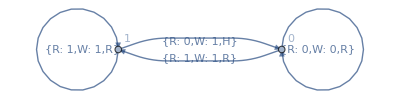

```mathematica
GraphPlotMachine[{
{0,0}->{0,0,1},
{0,1}->{1,1,1},
{1,0}->{0,1,0},
{1,1}->{1,1,1}
},
"ArrowheadSize"->0.05,
"VertexSize"->0.04
]
```

### Encoding

```mathematica
Concatenate[l_]:=Apply[Join,l];
ApplyCoding[digits_]:=Flatten[
IntegerDigits[digits,2]/.
{
1->{1,0},
"R"->{1,1,0},
"L"->{1,1,1,0},
"H"->{1,1,1,1,0}
}
];
Codify[instruction_]:=Map[ApplyCoding,instruction][[{"StateTo","Write","Direction"}]];

EncodeInstruction[<|"StateFrom"->_,"Read"->_,"StateTo"->0,"Write"->0,"Direction"->d_|>]:=ApplyCoding[d];
EncodeInstruction[<|"StateFrom"->_,"Read"->_,"StateTo"->0,"Write"->1,"Direction"->d_|>]:=Join[{1,0},ApplyCoding[d]];
EncodeInstruction[instruction_]:=Concatenate[Values[Codify[instruction]]];

EncodeProgram[program_]:=FromDigits[Drop[Concatenate[Map[EncodeInstruction,Drop[TuringProgramFormat[program],1]]],-3],2];
```

Nota: Un defecto de esta notación es que deja huecos. Toda máquina en cuya descripción haya más de cuatro símbolos 1, se denomina máquina no especificada correctamente.

```mathematica
allRules = Flatten[Outer[Rule,Drop[Tuples[{0,1},2],1],Flatten[Outer[Append,Tuples[{0,1},2],{-1,0,1},1],1],1],1]
```

{{0,1}→{0,0,-1},{0,1}→{0,0,0},{0,1}→{0,0,1},{0,1}→{0,1,-1},{0,1}→{0,1,0},{0,1}→{0,1,1},{0,1}→{1,0,-1},{0,1}→{1,0,0},{0,1}→{1,0,1},{0,1}→{1,1,-1},{0,1}→{1,1,0},{0,1}→{1,1,1},{1,0}→{0,0,-1},{1,0}→{0,0,0},{1,0}→{0,0,1},{1,0}→{0,1,-1},{1,0}→{0,1,0},{1,0}→{0,1,1},{1,0}→{1,0,-1},{1,0}→{1,0,0},{1,0}→{1,0,1},{1,0}→{1,1,-1},{1,0}→{1,1,0},{1,0}→{1,1,1},{1,1}→{0,0,-1},{1,1}→{0,0,0},{1,1}→{0,0,1},{1,1}→{0,1,-1},{1,1}→{0,1,0},{1,1}→{0,1,1},{1,1}→{1,0,-1},{1,1}→{1,0,0},{1,1}→{1,0,1},{1,1}→{1,1,-1},{1,1}→{1,1,0},{1,1}→{1,1,1}}

```mathematica
possible2RulePrograms = Map[Append[{{0,0}->{0,0,1}},#]&,allRules];
```

Las primeras 36 máquinas de Turing correctamente especificadas son:

```mathematica
correctas = Sort[Map[EncodeProgram,possible2RulePrograms]]
```

{0,1,2,3,4,5,6,9,10,11,13,19,21,26,27,43,52,53,54,105,106,107,109,211,213,218,219,427,436,437,873,874,875,1747,1749,3499}

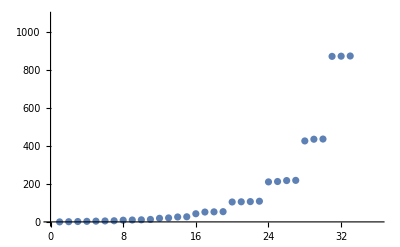

```mathematica
ListPlot[correctas]
```

El resto, es decir

```mathematica
Take[Complement[Range[Max[correctas]],correctas],100]
```

{7,8,12,14,15,16,17,18,20,22,23,24,25,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,44,45,46,47,48,49,50,51,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,108,110,111,112,113,114,115,116,117,118,119,120,121,122}

son  máquinas no especificadas correctamente.

### Decoding

```mathematica
Parse[l_,decoder_]:=Block[{f = decoder},
f[{}]:={Null,{}};
DeleteCases[FixedPointList[f[Last[#]]&,{Null,l}],{Null,_}][[All,1]]
];

TokenRecognizer[l_]:=Block[{takeNum},
takeNum = First[FirstPosition[l,0]];
{
Take[l,takeNum]/.
{
{0}-> 0,
{1,0}->1,
{1,1,0}->"R",
{1,1,1,0}->"L",
{1,1,1,1,0}->"H"
},
Drop[l,takeNum]
}
];

StatementRecognizer[l_]:=Block[{firstPosition},
firstPosition = FirstPosition[l,"L"|"R"|"H"];
{Take[l,First[firstPosition]],Drop[l,First[firstPosition]]}
];

StatementListFormat[statements_]:=Block[{firstPass,secondPass},
firstPass = ReplaceAll[statements,{{1,n_}:>{0,1,n},{n_}:>{0,0,n}}];
secondPass = Map[
{
FromDigits[Drop[#,-2],2],
#[[-2]],
#[[-1]] /.
{
"L"->-1,
"H"->0,
"R"->1
}
}&,
firstPass
];
Return[secondPass];
];

DecodeProgram[n_]:=Block[{binary,tokens,statements,formatted,leftInstructions,program,maxOneSequence},
binary = Join[IntegerDigits[n,2],{1,1,0}];
maxOneSequence = Max[Map[Length,SequenceSplit[binary,{0}]]];
If[maxOneSequence>4,Return[$Failed]];

tokens = Join[{0,0,"R"},Parse[binary,TokenRecognizer]];
statements = Parse[tokens,StatementRecognizer];
formatted = StatementListFormat[statements];

leftInstructions = Flatten[Outer[Append,Transpose[{Range[0,Ceiling[Length[formatted]/2]-1]}],{0,1},1],1];

program = Thread[Take[leftInstructions,Length[formatted]]->formatted];
Return[program];
];
```

Ejemplo UN+1

```mathematica
un1 = {
{0,0}->{0,0,1},
{0,1}->{1,1,1},
{1,0}->{0,1,0},
{1,1}->{1,1,1}
};
```

```mathematica
ProgramPrettify[un1]
```

{0^0→0_R^0,0^1→1_R^1,1^0→0_H^1,1^1→1_R^1}

```mathematica
EncodeProgram[un1]
```

177642

```mathematica
ProgramPrettify[DecodeProgram[177642]]
```

{0^0→0_R^0,0^1→1_R^1,1^0→0_H^1,1^1→1_R^1}

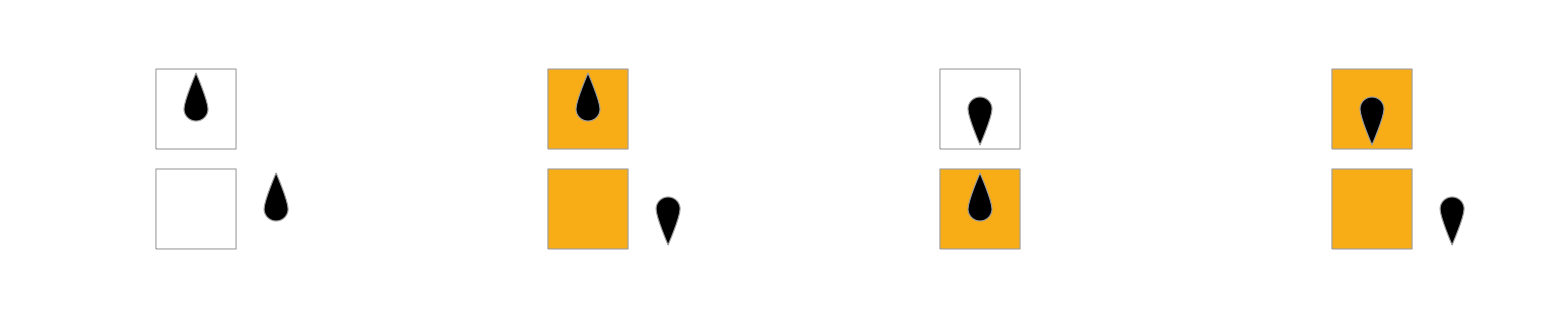

```mathematica
PlotMachineRules[un1]
```

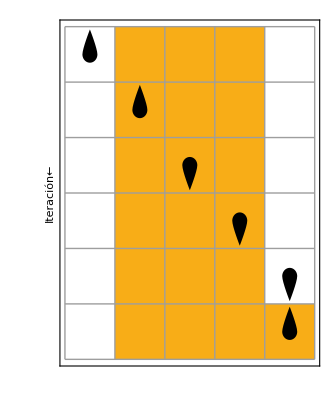

```mathematica
PlotMachineExecution[un1,0,{{1,1,1},0}]
```

```mathematica
HaltingProblem[un1,0,{{1,1,1},0}]
```

5

```mathematica
GraphPlotMachineExecution[
un1,
{{1,1,1},0},
HaltingProblem[un1,0,{{1,1,1},0}],
ImageSize->400,
"VertexSize"->0.05
]
```

## Codificación de los argumentos

### Encoding

```mathematica
argCoding = {
0->{0},
1->{1,0},
","->{1,1,0}
};
CodifyArg[n_Integer]:=Flatten[IntegerDigits[n,2]/.argCoding];
CodifyArg[s_String]:= s/.argCoding;
CodifyArg[l_List]:=Flatten[Map[CodifyArg,Riffle[l,","]]];

ArgumentExpansion[l_List]:=CodifyArg[l];
ArgumentExpansion[n_]:=Flatten[Map[CodifyArg,{n,","}]];

TapeEncode[n_]:={ArgumentExpansion[n],0};
```

```mathematica
TapeEncode[167]
```

{{1,0,0,1,0,0,0,1,0,1,0,1,0,1,1,0},0}

### Decoding

```mathematica
ArgTokenRecognizer[l_]:=Block[{firstMatch},
firstMatch = First[SequenceCases[l,{0}|{1,0}|{1,1,0}]];
{
firstMatch/.{
{0}->0,
{1,0}->1,
{1,1,0}->","
}
,
Drop[l,Length[firstMatch]]
}
];
TapeDecode[l_]:=Map[FromDigits[#,2]&,SequenceSplit[Parse[l,ArgTokenRecognizer],{","}]];
```

```mathematica
TapeDecode@{0,1,0,0,0,1,0,1,1,0,1,0,1,0,1,1,0,1,0,0,0,1,1,1,0,1,0,1,0,1,1,1,1,0,0,1,1,0}
```

{9,3,4,3,2}

```mathematica
TapeDecode@TapeEncode[167][[1]]
```

{167}

Ejemplo con XN+1

```mathematica
xn1 = {
{0,0}->{0,0,1},
{0,1}->{1,1,1},
{1,0}->{0,0,1},
{1,1}->{2,1,1},
{2,0}->{3,0,-1},
{2,1}->{2,1,1},
{3,0}->{0,1,0},
{3,1}->{4,0,-1},
{4,0}->{5,1,-1},
{4,1}->{4,1,-1},
{5,0}->{6,0,1},
{5,1}->{2,1,1},
{6,1}->{7,1,1},
{7,0}->{3,1,1},
{7,1}->{7,0,1}
};
```

```mathematica
ProgramPrettify[xn1]
```

{0^0→0_R^0,0^1→1_R^1,1^0→0_R^0,1^1→2_R^1,2^0→3_L^0,2^1→2_R^1,3^0→0_H^1,3^1→4_L^0,4^0→5_L^1,4^1→4_L^1,5^0→6_R^0,5^1→2_R^1,6^1→7_R^1,7^0→3_R^1,7^1→7_R^0}

```mathematica
EncodeProgram[xn1]
```

450813704461563958982113775643437908

```mathematica
ProgramPrettify[DecodeProgram[450813704461563958982113775643437908]]
```

{0^0→0_R^0,0^1→1_R^1,1^0→0_R^0,1^1→2_R^1,2^0→3_L^0,2^1→2_R^1,3^0→0_H^1,3^1→4_L^0,4^0→5_L^1,4^1→4_L^1,5^0→6_R^0,5^1→2_R^1,6^0→0_R^0,6^1→7_R^1,7^0→3_R^1,7^1→7_R^0}

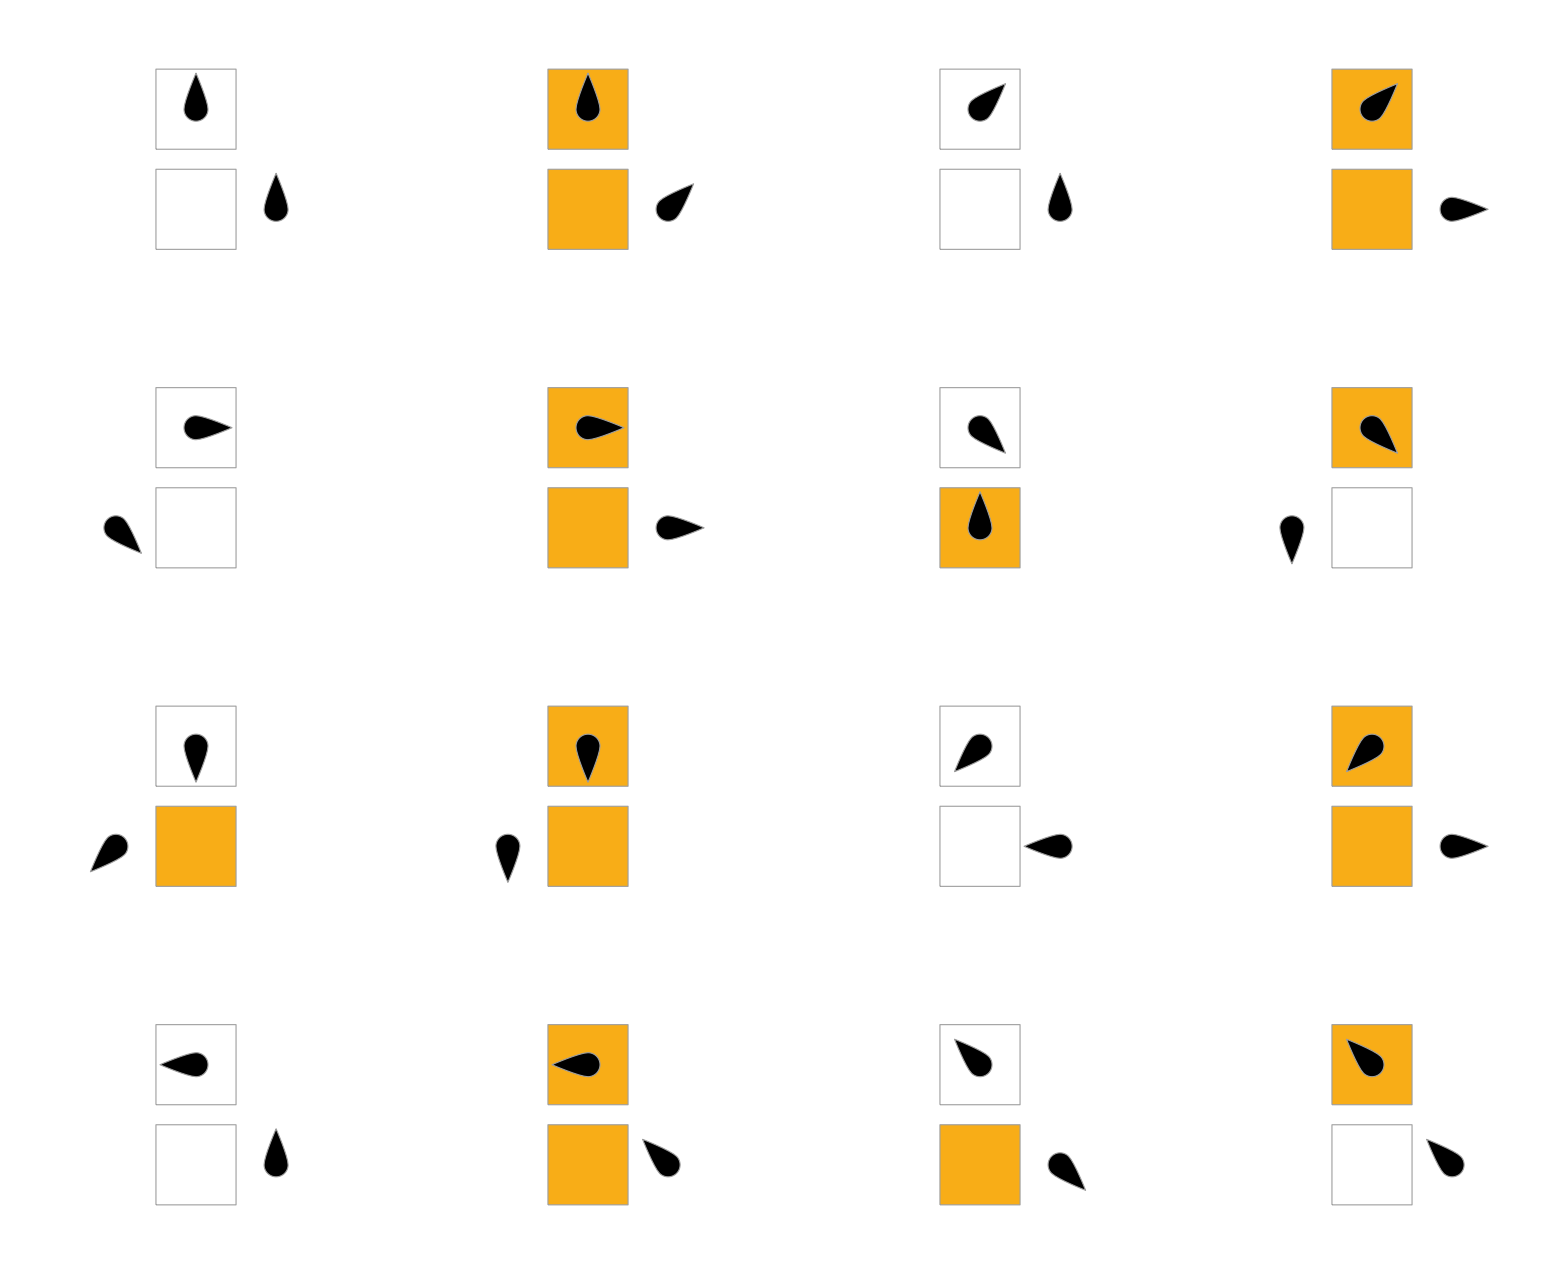

```mathematica
PlotMachineRules[program]
```

```mathematica
TapeDecode[MachineOutput[xn1,TapeEncode[167]]]
```

{168,0}

```mathematica
GraphPlotMachineExecution[
xn1,
TapeEncode[167],
HaltingProblem[xn1,0,TapeEncode[167]],
ImageSize->400,
"VertexSize"->0.05
]
```

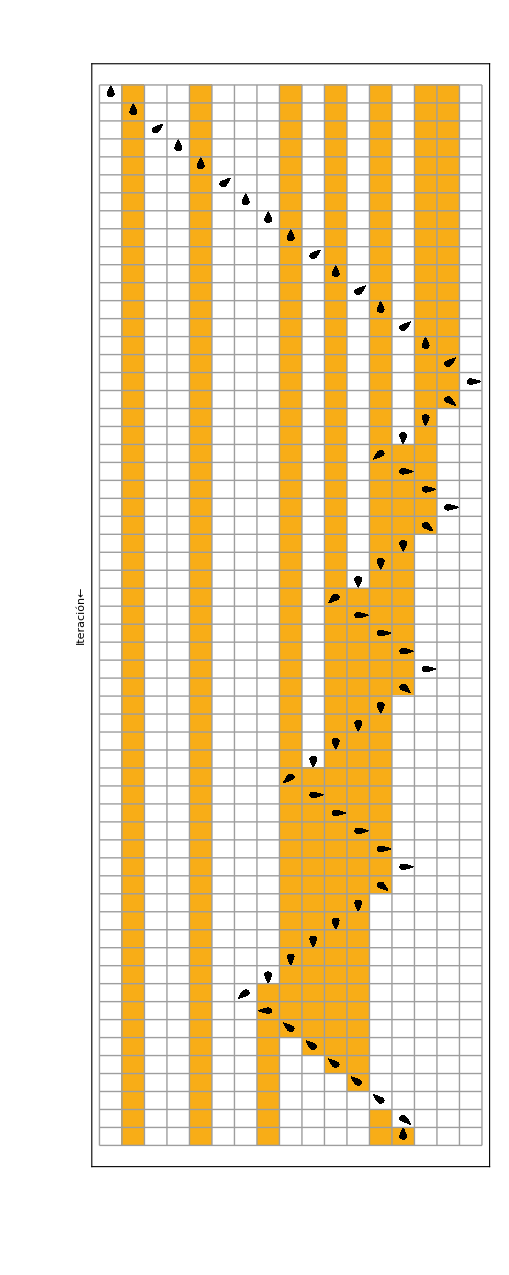

```mathematica
PlotMachineExecution[xn1,0,TapeEncode[167]]
```

## Primeras máquinas de turing

```mathematica
firstMachines = DeleteDuplicatesBy[DeleteCases[Map[{#,DecodeProgram[#]}&,Range[0,12]],{_,$Failed}],Last];
```

```mathematica
machinePlots = Map[GraphPlotMachine[Last[#],PlotLabel->First[#],ImageSize->200,"Legended"->False]&,firstMachines];
```

```mathematica
Rasterize@Grid[Partition[machinePlots,UpTo[4]]]
```

-Graphics-

## Pruebas de codificación

```mathematica
Map[{First[#],EncodeProgram[Last[#]]}&,DeleteCases[Map[{#,DecodeProgram[#]}&,Range[20]],{_,$Failed}]]
```

{{1,1},{2,2},{3,3},{4,4},{5,5},{6,6},{8,8},{9,9},{10,10},{11,11},{12,6},{13,13},{14,14},{16,16},{17,17},{18,18},{19,19},{20,20}}

```mathematica
DecodeProgram[6]
```

{{0,0}→{0,0,1},{0,1}→{0,0,1},{1,0}→{0,0,1}}

```mathematica
DecodeProgram[12]
```

{{0,0}→{0,0,1},{0,1}→{0,0,1},{1,0}→{0,0,1}}

## Máquina Universal

```mathematica
u = 7244855335339317577198395039615711237952360672556559631108144796606505059404241090310483613632359365644443458382226883278767626556144692814117715017842551707554085657689753346356942478488597046934725739988582283827795294683460521061169835945938791885546326440925525505820555989451890716537414896033096753020431553625034984529832320651583047664142130708819329717234151056980262734686429921838172157333482823073453713421475059740345184372359593090640024321077342178851492760797597634415123079586396354492269159479654614711345700145048167337562172573464522731054482980784965126988788964569760906634204477989021914437932830019493570963921703904833270882596201301773727202718625919914428275437422351355675134084222299889374410534305471044368695876405178128019437530813870639942772823156425289237514565443899052780793241144826142357286193118332610656122755531810207511085337633806031082361675045635852164214869542347187426437544428790062485827091240422076538754264454133451748566291574299909502623009733738137724162172747723610206786854002893566085696822620141982486216989026091309402985706001743006700868967590344734174127874255812015493663938996905817738591654055356704092821332221631410978710814599786695997045096818419062994436560151454904880922084480034822492077304030431884298993931352668823496621019471619107014619685231928474820344958977095535611070275817487333272966789987984732840981907648512726310017401667873634776058572450369644348979920344899974556624029374876688397514044516657077500605138839916688140725455446652220507242623923792115253181625125363050931728631422004064571305275802307665183351995689139748137504926429605010013651980186945639498;
utm = DecodeProgram[u];
```

```mathematica
UTMTape[program_,argument_]:={Join[IntegerDigits[program,2],{1,1,1,1,1,0},argument],0};
UTMResult[program_,argument_,maxIterations_]:=Block[{lastStep,tape,cursorPos},
lastStep = Last[TuringMachine[program,{{0,0},argument},maxIterations]];
tape = Last[lastStep];
cursorPos = First[lastStep][[2]];
Take[tape,cursorPos+1]
];
```

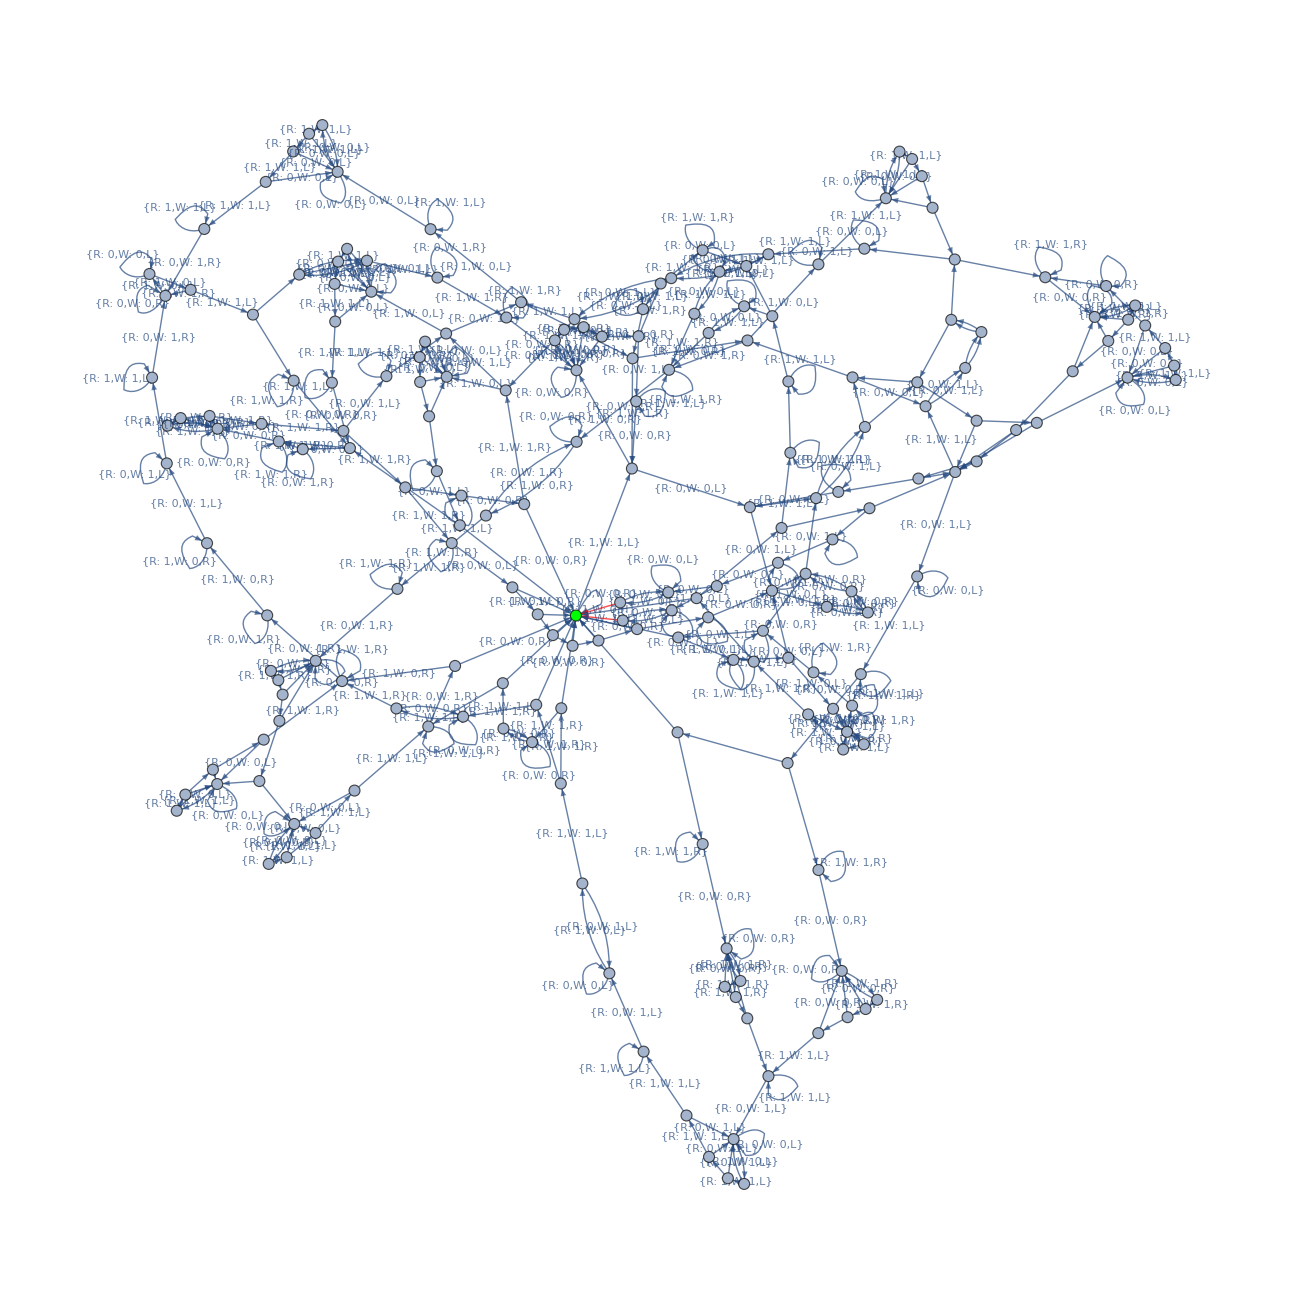

```mathematica
haltInstructionPositions = Position[utm[[All,2]],{_,_,0}];
graphData = GraphPlotMachineExecutionProgramFormat[utm];
Graph[MapAt[Style[#,Red]&,graphData,haltInstructionPositions],VertexStyle->{0->Green},ImageSize->1300,VertexLabels->"Name"]
```

Emulación de UN+1

```mathematica
un1UtmCoded = UTMTape[177642,{1,1,1}]
```

{{1,0,1,0,1,1,0,1,0,1,1,1,1,0,1,0,1,0,1,1,1,1,1,0,1,1,1},0}

```mathematica
HaltingProblem[utm,0,un1UtmCoded,10000]
```

3302

```mathematica
lastStep = Last[TuringMachine[utm,{{0,0},un1UtmCoded},3302]]
```

{{0,5,-19},{0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,1,0,1,1,0,1,0,1,1,1,1,0,1,0,1,0,1,1,0,1,1,1,1,1}}

```mathematica
UTMResult[utm,un1UtmCoded,3302]
```

{0,1,1,1,1,0}

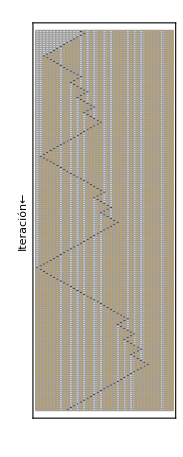

```mathematica
PlotMachineExecution[utm,0,un1UtmCoded,"MaxIterations"->200]
```

```mathematica
GraphPlotMachineExecution[utm,un1UtmCoded,3302,ImageSize->1200,"ArrowheadSize"->0.01,"Labeled"->False]
```

```mathematica
(*
Nota: Crear directorio primero.
ExportGraphPlotMachineExecutionFrames[FileNameJoin[{NotebookDirectory[],"frames","utm.png"}],utm,un1UtmCoded,3302];
*)
```

Descripción:
248 -> fetch argument 0
484 -> write argument 0
531 -> fetch argument 1
916 -> write argument 1
964 -> fetch argument 2
1817 -> write argument 2
1865 -> fetch argument 3
2718 -> write argument 3
2766 -> fetch argument 4
3301 -> write argument 4

Emulación de XN+1

```mathematica
xn1UtmCoded = UTMTape[450813704461563958982113775643437908,First[TapeEncode[167]]]
```

{{1,0,1,0,1,1,0,1,1,0,1,0,0,1,0,1,1,0,1,0,1,0,0,1,1,1,0,1,0,0,1,0,1,1,0,1,0,1,1,1,1,0,1,0,0,0,0,1,1,1,0,1,0,0,1,0,1,0,1,1,1,0,1,0,0,0,1,0,1,1,1,0,1,0,1,0,0,0,1,1,0,1,0,0,1,0,1,1,0,1,1,0,1,0,1,0,1,0,1,0,1,1,0,1,0,1,0,1,0,1,1,0,1,0,1,0,1,0,0,1,1,1,1,1,0,1,0,0,1,0,0,0,1,0,1,0,1,0,1,1,0},0}

```mathematica
HaltingProblem[utm,0,xn1UtmCoded,500000]
```

156961

```mathematica
rawResult = UTMResult[utm,xn1UtmCoded,156961]
```

{0,1,0,0,1,0,0,1,0,0,0,0,1,1,0}

```mathematica
TapeDecode[rawResult]
```

{168}

## Problema de la indecibilidad

```mathematica
H[n_,m_,maxIterations_]:=Block[{program,preprocessed,iterations,isThereHalt},
program = DecodeProgram[n];
If[program === $Failed,Return["□"]];
preprocessed = PreprocessProgram[program];
isThereHalt = MemberQ[program[[All,2]],{_,_,0}];
If[!isThereHalt,Return[0]];

iterations = Length[
NestWhileList[
TuringMachine[
preprocessed,#
]&,
{{0,0,0},{IntegerDigits[m,2],0}},
UnsameQ[#1[[1,-1]],#2[[1,-1]]]&,2,
maxIterations
]
]-1;

If[iterations<maxIterations,
Return[1],
Return["□"]
];
];

T[n_,m_,iterations_]:=Block[{program,preprocessed,tape},
program = DecodeProgram[n];
preprocessed = PreprocessProgram[program];
tape = {IntegerDigits[m,2],0};

FromDigits[ExecuteMachine[preprocessed,tape,0,iterations][[-1,-1]],2]
];

HaltingIterations[n_,m_,maxIterations_:100]:=HaltingProblem[DecodeProgram[n],0,{IntegerDigits[m,2],0},maxIterations];

TuringMatrixElement[n_,m_]:=Block[{h,maxIterations = 100},
h = H[n,m,maxIterations];
If[h == "□" || h == 0,Return[h]];

T[n,m,HaltingIterations[n,m,maxIterations]]
];
```

```mathematica
size = 30;
qnm = Table[TuringMatrixElement[i,j],{i,0,size},{j,0,size}];
```

```mathematica
MatrixForm[qnm]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
□ | 0 | 0 | 1 | 0 | 1 | 2 | 3 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
□ | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
□ | 0 | 0 | 1 | 0 | 1 | 2 | 3 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
□ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □ | □
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
□ | 0 | 0 | 1 | 0 | 1 | 2 | 3 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14)

Debe existir una máquina de Turing T_k capaz de generar la secuencia computable:

```mathematica
diagonalCut = Map[If[# == "□","□",#+1]&,Diagonal[matrix]]
```

{1,1,1,2,1,1,1,□,1,1,1,12,1,1,1,□,1,1,1,4,1,1,1,□,1,1,1,□,1,1,15}

de hecho es posible definir una función que se comporte como dicha máquina.

```mathematica
Tk[n_]:=TuringMatrixElement[n,n]+1/.{(_+"□")->"□"};
```

```mathematica
Map[Tk,Range[0,size]]
```

{1,1,1,2,1,1,1,□,1,1,1,12,1,1,1,□,1,1,1,4,1,1,1,□,1,1,1,□,1,1,15}

Supongase que n = k, entonces  debido a que 1+T_k(k) H(k;k) = T_k(k) debe ocurrir que T_k(k) = □, y al mismo tiempo para evitar la relación 1+0 = □  es necesario que H(k;k) = □.